## State

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
MatrixForm[w=ImportArmaBinary["w.bin"][[1]]];
MatrixForm[w0=ImportArmaBinary["w0.bin"][[1]]];
MatrixForm[psi=ImportArmaBinary["psi.bin"]];
```

```mathematica
dispersion[dmu_,t1_,t2_,t3_,t4_]:=Compile[{{kx,_Real,0},{ky,_Real,0}},
Module[{h},
h=Table[0.,{2},{2}];
h[[1,1]]=-2t1 Cos[ky]-2t4 Cos[kx]-1/2dmu;
h[[2,2]]=-2t1 Cos[kx]-2t4 Cos[ky]+1/2dmu;
h[[1,2]]=-4t2 Cos[kx/2]Cos[ky/2]-4t3(Cos[kx/2]Cos[3ky/2]+Cos[3kx/2]Cos[ky/2]);
h[[2,1]]=h[[1,2]];
Sort[Eigenvalues[h]]
],{{Eigenvalues[__],_Real,1}}
]
```

```mathematica
dmu=0.;t1=1.;t2=0.3;t3=0.;t4=1.0;L=10;Nf=38(*Nu+Nd*);
eps=dispersion[dmu,t1,t2,t3,t4];
w=Flatten[Table[eps[2Pi i/L,2Pi j/L],{i,1,L},{j,1,L}]];
w1=RankedMin[w,Floor[Nf/2]];
w2=RankedMin[w,Floor[Nf/2]+1];
mu=(w1+w2)/2;
RegionPlot[
{First[eps[kx,ky]]<mu,Last[eps[kx,ky]]<mu},{kx,-Pi,Pi},{ky,-Pi,Pi},
Epilog->{Point[Flatten[Table[{2Pi i/L,2Pi j/L},{i,-L,L},{j,-L,L}],1]]},
PlotPoints->50
]
Row[{"gap: ",Chop[w2-w1]}]
Row[{"mu: ",10mu/StandardDeviation[w]}]
Clear[dmu,t1,t2,t3,t4,eps,L,Nf,mu,w1,w2]
```

```mathematica
labelDegeneracy[w_]:=Module[{rw,f,map,i,j,k,c,res},
f=100000;
map={};
c={};
res={};
j=1;
Do[
rw=Round[f w[[i]]];
k=rw/.map;
If[k==rw,
AppendTo[map,rw->j];
AppendTo[c,-1];
k=j;
j++;
];
c[[k]]++;
AppendTo[res,{w[[i]],c[[k]]}]
,{i,1,Length[w]}];
res
]
```

```mathematica
<<ArmaBinary`
eta=0.02;beta=50;
SetDirectory[NotebookDirectory[]];
Ju=ImportArmaBinary["Jd.bin"]+1;
w=ImportArmaBinary["w.bin"][[1]]/beta;
wd=labelDegeneracy[w].{1,eta};
levels=Tally[w,Abs[#1-#2]<1.*^-8&];
levels=Flatten[Table[#[[1]]+eta (i-1),{i,1,#[[2]]}]&/@levels];
ListPlot[Transpose[Sort[wd[[#]]]&/@Ju],
ImageSize->800,GridLines->{None,levels},PlotStyle->Directive[Black,AbsolutePointSize[5]](*,
PlotRange->{-1.4,-1.35}*)

]
```

## Rotate face

```mathematica
plotParticles[p0_]:=Module[{p,q, L,x,y,Nf},
L=Sqrt[Length[p0]/2];
p=ArrayReshape[p0,{L,L,2}];
Nf=(Max[p]-1)/2;
Graphics[{
Table[
{
q=p[[y+1,x+1,1]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x+1,y}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2,{x+0.5,y},{0,-1.5}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2-Nf,{x+0.5,y},{0,-1.5}]}
],
q=p[[y+1,x+1,2]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x,y+1}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2,{x,y+0.5},{-1.5,0}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2-Nf,{x,y+0.5},{-1.5,0}]}
]
}
,{x,0,L-1},{y,0,L-1}],
Black,
Table[
Text[x+L*y,{x+0.5,y+0.5}]
,{x,0,L-1},{y,0,L-1}]
},
BaseStyle->{FontSize->12},
ImageSize->300
]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
p=ImportArmaBinary["p.bin"];
GraphicsRow[plotParticles/@p]
```

## Correct distribution

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
p=ImportArmaBinary["p.bin"];
ListPlot[p,PlotStyle->AbsolutePointSize[1]]
```

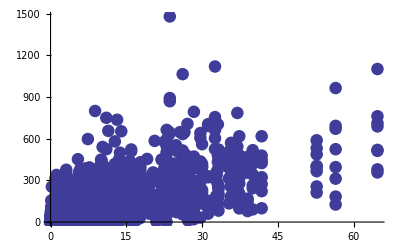

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->{All,{0,All}},PlotStyle->{AbsolutePointSize[3]}]
```

```mathematica
Select[tally,Norm[#[[1]]-tally[[4,1]]]<1.*^-7&]
```

```mathematica
w=Flatten[Table[i,{i,1,6},{RandomInteger[{100,200}]}]];
w=Table[Random[],{200}];
b=Accumulate[w];
b=N[b/Max[b]];
ls=Table[
x=Random[];
i=1;
While[i<=Length[b]&&b[[i]]<x,i++];
i
,{5000}];
tally=Tally[ls];
ListPlot[Transpose[{w[[tally[[All,1]]]],tally[[All,2]]}]]
Clear[w,b,ls,i,x]
```

## Swap states

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->All]
```

## Measure operators

```mathematica
observables={"boson_hopping","fermion_hopping_1","fermion_hopping_2","fermion_hopping_3"};
parameters={"dmu","t1","t2","t3","t4"};
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
<<ErrorBarPlots`
EE=ImportArmaBinary["E1_t2_beta.bin"];
EE=Map[Select[#,#[[1]]≠0.&]&,EE,{1}];
Row[{ErrorListPlot[EE,ImageSize->400,Joined->True],Spacer[100],TableForm[Table[Style[observables[[i]],ColorData[1,i]],{i,1,Length[observables]}]]}]
Clear[EE]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
G=ImportArmaBinary["G_t2_beta.bin"];
sG=ImportArmaBinary["sG_t2_beta.bin"];
<<ErrorBarPlots`
i=4;
Row[{ErrorListPlot[Transpose[{G,sG},{4,1,3,2}][[i]],
Joined->True,ImageSize->400,PlotLabel->observables[[i]],PlotRange->All],
Spacer[100],
TableForm[Table[Style[parameters[[i]],ColorData[1,i]],{i,1,Length[parameters]}]]}]
i=3;
Row[{ErrorListPlot[Transpose[{G,sG},{4,2,3,1}][[i]],
PlotLabel->parameters[[i]],Joined->True,ImageSize->400,PlotRange->All],
Spacer[100],
TableForm[Table[Style[observables[[i]],ColorData[1,i]],{i,1,Length[observables]}]]}]
Clear[G,sG,i]
```